```mathematica
pts={{0.0, 0.8810487},{0.5,0.52062547},{1.0,0.32412635},{2.0,0.15319098}} (*these are the points I found in python in the format {redshift, growth}*)
```

{{0.,0.881049},{0.5,0.520625},{1.,0.324126},{2.,0.153191}}

```mathematica
(*use NDSolve to solve our diffeq in terms of u = ln(a). also there was a sign error in the equation in the pset!!*)
```

```mathematica
s=NDSolve[{g''[u]+(5/2+3/2 ΩDE)g'[u]+3ΩDE g[u]==0/.ΩDE->1/(1+(Exp[u]/aΛm)^-3)/.aΛm->0.77,g[-5]==1,g'[-5]==0},g,{u,-5,0}]
```

{{g→InterpolatingFunction[…]}}

```mathematica
(g/.s[[1]])[-0.001](*check the growth value close to zero and make sure we get close to 0.78!*)
```

0.787285

```mathematica
(*plot the growth function along with the four points we calculated from the data in python - it's not a bad fit*)
```

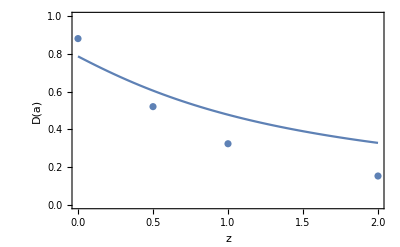

```mathematica
Module[{a,u},Show[Plot[(a=1/(1+z);u=Log[a];a g[u])/.s[[1]],{z,0,2},PlotRange->{{0,2},{0,1}},Frame->True,FrameLabel->{"z","D(a)"}],ListPlot[pts]]]
```